```mathematica
(*Calculations for graph states. Derives the local Pauli measurement outcomes*)
pm=PauliMatrix
single[n_,switch_,matrix_]:= (*n: number of qubits. switch: qubit to apply matrix to*)KroneckerProduct@@ReplacePart[ConstantArray[IdentityMatrix[2],n],switch->matrix];
czGate[n_,control_,target_]:= Divide[1,2](IdentityMatrix[2^n]+single[n, control, pm[3]]+single[n,target,pm[3]]-single[n, control, pm[3]].single[n,target,pm[3]]);
```

PauliMatrix

```mathematica
id=pm[0];
x=pm[1];
y=pm[2];
z=pm[3];
```

```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
bra0=Transpose[ket0];
bra1=Transpose[ket1];
ketPlus=1/Sqrt[2](ket0+ket1);
ketMinus=1/Sqrt[2](ket0-ket1);
ketPlusT=1/Sqrt[2](ket0+I ket1);
ketMinusT=1/Sqrt[2](ket0-I ket1);
nq=3
```

3

```mathematica
rho=czGate[nq, 1,3].czGate[nq, 1,2].KroneckerProduct[ketPlus,ketPlus, ketPlus]
```

{{1/(2 √2)},{1/(2 √2)},{1/(2 √2)},{1/(2 √2)},{1/(2 √2)},{-1/(2 √2)},{-1/(2 √2)},{1/(2 √2)}}

```mathematica
xP1=ketPlus.Transpose[ketPlus]
xM1=ketMinus.Transpose[ketMinus]
```

{{1/2,1/2},{1/2,1/2}}

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
(*Matrix function from Hein graph paper*)
sigmaJ[m_]:=ExpToTrig[MatrixExp[+I Pi/4 m]]
```

```mathematica
FullSimplify[sigmaJ[y]] (*U_(x,+)^a H\times x*)
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
FullSimplify[sigmaJ[-y]] (*U_(x,-)^a x\times H*)
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
sigmaJ[z](*U_{y,-}^a  (1+I)/sqrt(2)S^dag*)
```

{{(1+ⅈ)/(√2),0},{0,(1-ⅈ)/(√2)}}

```mathematica
sigmaJ[-z](*U_{y,+}^a  (1-I)/sqrt(2)S*)
```

{{(1-ⅈ)/(√2),0},{0,(1+ⅈ)/(√2)}}

```mathematica
h.x
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
x.h
```

{{1/(√2),-1/(√2)},{1/(√2),1/(√2)}}

```mathematica
FullSimplify[ExpToTrig[sigmaJ[z]]==1/Sqrt[2]{{1+I,0},{0, 1-I}}]
```

True

```mathematica
Plot[Log[4^n],2n,{n,0,20}]
```

Plot::nonopt: Options expected (instead of {n,0,20}) beyond position 2 in Plot[Log[4^n],2 n,{n,0,20}]. An option must be a rule or a list of rules.

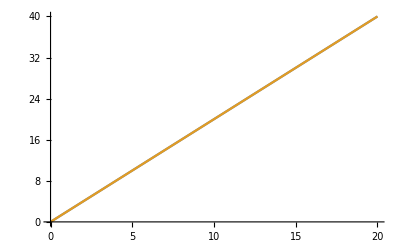

```mathematica
Plot[{Log[2,4^n],2 n},{n,0,20}]
```